```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry`
```

t::shdw: Symbol t appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

f::shdw: Symbol f appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

a::shdw: Symbol a appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

v::shdw: Symbol v appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

s::shdw: Symbol s appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

y::shdw: Symbol y appears in multiple contexts {Geometry`,NumberTheory`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

q::shdw: Symbol q appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

w::shdw: Symbol w appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {Geometry`,NumberTheory`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

r::shdw: Symbol r appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

q$::shdw: Symbol q$ appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

x$::shdw: Symbol x$ appears in multiple contexts {Geometry`,Global`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

out::shdw: Symbol out appears in multiple contexts {Geometry`,NumberTheory`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

out$::shdw: Symbol out$ appears in multiple contexts {Geometry`,NumberTheory`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

tf::shdw: Symbol tf appears in multiple contexts {Geometry`,NumberTheory`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

mf::shdw: Symbol mf appears in multiple contexts {Geometry`,NumberTheory`}; definitions in context Geometry` may shadow or be shadowed by other definitions.

## TEST1

### Case 1

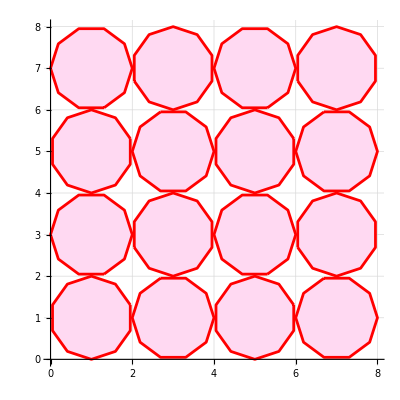

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[10,RGBColor[1,.85,.95,.1]][[1]],{1,1}],{Red,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr1
```

### Case 2

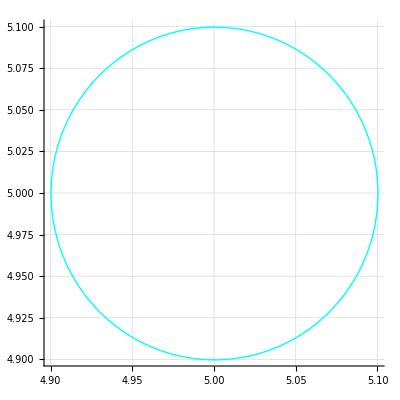

```mathematica
cCircle[{5,5},.1]//toGL//gr1
```

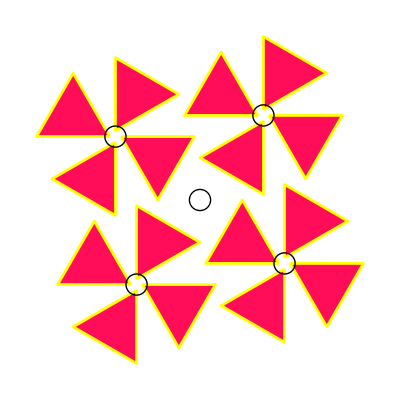

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.25,0},{0.5,0.25},{0.5,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
sym4rot[sym4ref[dpoly]]//toGL//gr1
```

-Graphics-

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Case 4 ( IN-DEVELOPMENT )

```mathematica
dpoly0:={{{1,{{0.25,0.0},{0.5,0.0},{0.5,0.75},{0.75,0.75},{0.75,1.0},{0.0,1.0},{0.0,0.75},{0.25,0.75}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyA:={{{1,{{0.5,0},{1,0.5},{1,1},{0.5,0.5},{0,1},{0,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{0,0},{0.5,0},{0,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyC:={{{1,{{0.5,0},{1,0},{1,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={dpolyA,dpolyB,dpolyC}
dpoly//toGL//gr1;
sym4ovr1[dpoly]//toGL//gr1
```

-Graphics-

```mathematica
sym4ovr1[figke_]:=Module[{rotp},
rotp={1,1};
tra3[Scale[
{
figke,
rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],
tra3[figke,{1,1}],
tra3[rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],{-1,1}]
},
.5],{-.5,-.5}]]
```

```mathematica
ind:=Tuples[Composition@@{sym4rot,sym4ref,sym4ovr1},3]
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ind//TableForm
```

sym4rot@*sym4rot@*sym4rot
sym4rot@*sym4rot@*sym4ref
sym4rot@*sym4rot@*sym4ovr1
sym4rot@*sym4ref@*sym4rot
sym4rot@*sym4ref@*sym4ref
sym4rot@*sym4ref@*sym4ovr1
sym4rot@*sym4ovr1@*sym4rot
sym4rot@*sym4ovr1@*sym4ref
sym4rot@*sym4ovr1@*sym4ovr1
sym4ref@*sym4rot@*sym4rot
sym4ref@*sym4rot@*sym4ref
sym4ref@*sym4rot@*sym4ovr1
sym4ref@*sym4ref@*sym4rot
sym4ref@*sym4ref@*sym4ref
sym4ref@*sym4ref@*sym4ovr1
sym4ref@*sym4ovr1@*sym4rot
sym4ref@*sym4ovr1@*sym4ref
sym4ref@*sym4ovr1@*sym4ovr1
sym4ovr1@*sym4rot@*sym4rot
sym4ovr1@*sym4rot@*sym4ref
sym4ovr1@*sym4rot@*sym4ovr1
sym4ovr1@*sym4ref@*sym4rot
sym4ovr1@*sym4ref@*sym4ref
sym4ovr1@*sym4ref@*sym4ovr1
sym4ovr1@*sym4ovr1@*sym4rot
sym4ovr1@*sym4ovr1@*sym4ref
sym4ovr1@*sym4ovr1@*sym4ovr1